## Generating Fourier Coefficients for an Imperfect (Asymmetric) Grating Function

### Graphing what a single slit of the perfect grating structure looks like :

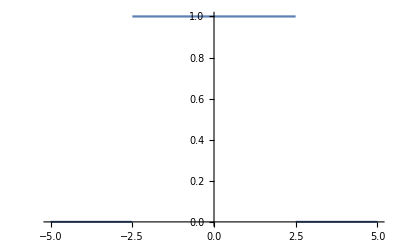

```mathematica
Gratings = Piecewise[{{0, x<-25*10^(-9) && x>-50*10^(-9)},{1, x<25*10^(-9) && x>-25*10^(-9)},{0, x>25*10^(-9) && x<50*10^(-9)}},0];
Plot[Gratings, {x, -50*10^(-9), 50*10^(-9)}]
```

This has a period of 100 nm, with slits 50 nm wide and 50 nm of separation

### Graphing an imperfect grating structure

Now model non - uniform separation
45 nm and 55 nm alternating separation

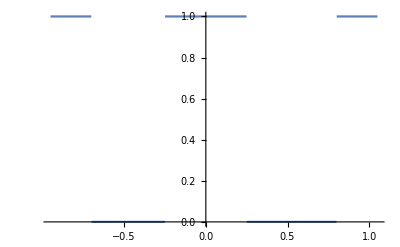

```mathematica
Gratings2 = Piecewise[{{1,x> -95*10^(-9)&&x<-70*10^(-9)},{0, x<-25*10^(-9) && x>-70*10^(-9)},{1, x<25*10^(-9) && x>-25*10^(-9)},{0, x>25*10^(-9) && x<80*10^(-9)},{1, x>80*10^(-9) && x<105*10^(-9)}},0];
Plot[Gratings2, {x, -95*10^(-9), 105*10^(-9)}]
```

We maintain the same open fraction (.5), but some slits are now offset by 5 nm
We’ve had to graph two slits over a range -95 nm to 105 nm
Center our function over -100 nm to 100 nm:

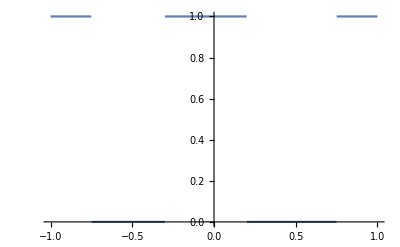

```mathematica
Gratings3 = Piecewise[{{1,x> -100*10^(-9)&&x<-75*10^(-9)},{0, x<-30*10^(-9) && x>-75*10^(-9)},{1, x<20*10^(-9) && x>-30*10^(-9)},{0, x>20*10^(-9) && x<75*10^(-9)},{1, x>75*10^(-9) && x<100*10^(-9)}},0];
Plot[Gratings3, {x, -100*10^(-9), 100*10^(-9)}]
```

The middle slit has center at - 5 nm
Although the slits are the same size (50 nm) our function is no longer repeating with a period of 100 nm
Our function repeats every 200 nm, so we now use d = 200 nm when calculating our Fourier components

### The fourier components

Define  fc = 2*Pi*n*ex/d, then sum Cos[fc] and Sin[fc] for each n value (ints from - 20 to 20) over a certain number of values of ex (on the interval where the slit is open/has a value of 1) determined by the variable res .  The cos sum for each n is placed in a matrix to contain real values (ReT) and the sin terms are placed in ImT . The sums are then divided by res
This should approximate the integral of F (x)*e^(2 Pi*n*x/d) over the period, where F (x) is a square wave representing the grating - which is the formula to find the coefficients of the Fourier series representing F(x)

Following this procedure:

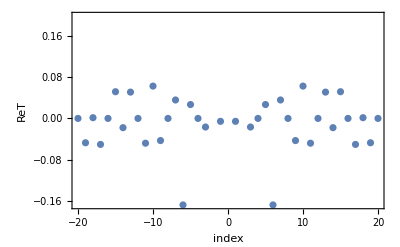

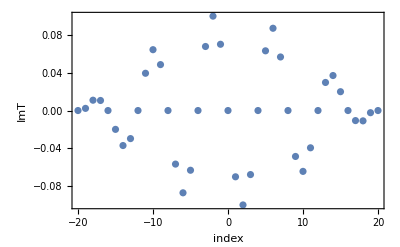

```mathematica
ReT=Transpose[{-20+(#-1)&/@Range[41],ConstantArray[0,41]}]; (* ReT matrix holds the real components of the Fourier coefficients for n values from -20 to 20, not yet filled it*)
ImT = ReT; (*Same as above for the imaginary components*)
res=1000;(* number of terms summed to find the coefficients *)
d = 200*10^(-9); (*new period is 200 nm*)
nu = 0.5; (* open fraction, 50% of grating is open *)
width = nu*d; (* open fraction times period gives open width in a period, this now gives double the width of a slit AKA the total width of two slits *)

(*locations of edges of slits, start and end points for sums *)
(*first half slit*)
minslit1 = -100*10^(-9);
maxslit1 = -75*10^(-9);
(*middle/full slit*)
minslit2 = -30*10^(-9);
maxslit2 = 20*10^(-9);
(*third slit, half*)
minslit3 = 75*10^(-9);
maxslit3 = 100*10^(-9);

x2pnt[arr__,n_]:=Position[arr[[All,1]],n][[1]][[1]](*this is a function that is used to return index where n occurs in the index of ImT or ReT*)

increment = width/res; 

(* we're breaking up the Do loop into separate sums for each slit *)
Do[
(* this does the sum for the first slit *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit1,maxslit1-increment, increment}];

Do[
(* now add the second slit *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit2,maxslit2-increment, increment}];

Do[
(* and the third *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit3,maxslit3-increment, increment}];

(* each of the fourier terms in each array are divided by res *) 
 ReT[[All,2]]/=res;
ImT[[All,2]]/=res;  

(* Plot the terms *)
ListPlot[ReT,Frame->True,FrameLabel->{"index","ReT"}]
ListPlot[ImT,Frame->True,FrameLabel->{"index","ImT"}]
```

We now have new ReT and ImT matrices holding Fourier coefficients for a non - uniform grating